```mathematica
Index[p_,t_]:=1+(2.7785 10^-4) *(p(1+p(60.1 - 0.972 t) 10^-10))/(96095.43(1+.003661t));
RE=6.371 10^6;
p[r_]:=QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-RE,"Meters"],"Pressure"],"Pascals"]];
t[r_]:=QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-RE,"Meters"],"Temperature"],"Celsius"]];
Index[r_]:=1+((2.7785 10^-4) p[r](1+p[r](60.1 - 0.972 t[r])10^-10))/(96095.43(1+.003661t[r]));
```

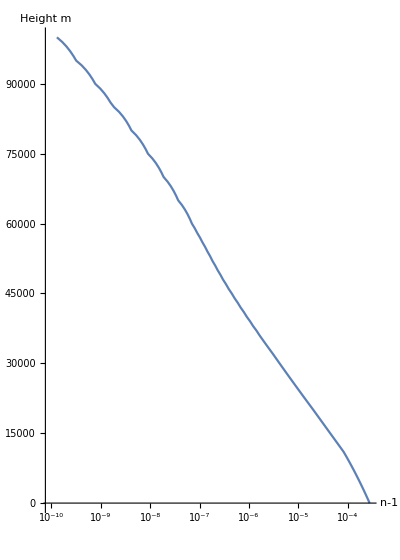

```mathematica
ListLogLinearPlot[
Table[{Index[x+RE]-1,x},{x,0,100000,1000}],AxesLabel->{n-1,Height(m)},Joined->True,GridLines->Automatic,AspectRatio->1.4]
```

```mathematica
Table[{x,r=RE;phi0=x;phi=phi0;theta=0;dr=0;
While[r<RE+100000,
r=r+dr;
dr=Ceiling[r-RE+.01]/10;
theta=theta+Pi/2-phi-ArcSin[r/(r+dr)Cos[phi]];
phi=ArcCos[Index[r]/Index[r+dr]*r/(r+dr)Cos[phi]];];theta-phi+phi0},{x,0,Pi/2,Pi/180}]
(* this one takes a long time! don't run multiple times *)
(* Ceiling[r-RE+0.1]/10 is there to decrease the increment for lower values of r, this increases precision without sacrificing too much computation power*)
```

{{0,0.00928885},{π/180,0.00671692},{π/90,0.0051041},{π/60,0.00404762},{π/45,0.0033197},{π/36,0.002796},{π/30,0.00240515},{(7 π)/180,0.00210427},{(2 π)/45,0.00186651},{π/20,0.00167442},{π/18,0.00151628},{(11 π)/180,0.00138397},{π/15,0.00127171},{(13 π)/180,0.0011753},{(7 π)/90,0.00109161},{π/12,0.00101829},{(4 π)/45,0.000953501},{(17 π)/180,0.000895831},{π/10,0.00084415},{(19 π)/180,0.000797555},{π/9,0.000755313},{(7 π)/60,0.000716825},{(11 π)/90,0.000681596},{(23 π)/180,0.000649213},{(2 π)/15,0.00061933},{(5 π)/36,0.000591655},{(13 π)/90,0.000565937},{(3 π)/20,0.000541964},{(7 π)/45,0.000519553},{(29 π)/180,0.000498543},{π/6,0.000478796},{(31 π)/180,0.000460192},{(8 π)/45,0.000442624},{(11 π)/60,0.000425999},{(17 π)/90,0.000410234},{(7 π)/36,0.000395254},{π/5,0.000380996},{(37 π)/180,0.0003674},{(19 π)/90,0.000354413},{(13 π)/60,0.000341988},{(2 π)/9,0.000330083},{(41 π)/180,0.000318658},{(7 π)/30,0.00030768},{(43 π)/180,0.000297116},{(11 π)/45,0.000286937},{π/4,0.000277117},{(23 π)/90,0.000267631},{(47 π)/180,0.000258457},{(4 π)/15,0.000249576},{(49 π)/180,0.000240967},{(5 π)/18,0.000232614},{(17 π)/60,0.000224501},{(13 π)/45,0.000216612},{(53 π)/180,0.000208935},{(3 π)/10,0.000201455},{(11 π)/36,0.000194162},{(14 π)/45,0.000187044},{(19 π)/60,0.000180091},{(29 π)/90,0.000173293},{(59 π)/180,0.000166641},{π/3,0.000160126},{(61 π)/180,0.000153741},{(31 π)/90,0.000147477},{(7 π)/20,0.000141328},{(16 π)/45,0.000135287},{(13 π)/36,0.000129347},{(11 π)/30,0.000123503},{(67 π)/180,0.000117749},{(17 π)/45,0.000112079},{(23 π)/60,0.000106488},{(7 π)/18,0.000100971},{(71 π)/180,0.0000955236},{(2 π)/5,0.0000901409},{(73 π)/180,0.0000848187},{(37 π)/90,0.0000795527},{(5 π)/12,0.000074339},{(19 π)/45,0.0000691736},{(77 π)/180,0.0000640528},{(13 π)/30,0.000058973},{(79 π)/180,0.0000539306},{(4 π)/9,0.0000489221},{(9 π)/20,0.0000439442},{(41 π)/90,0.0000389937},{(83 π)/180,0.0000340674},{(7 π)/15,0.000029162},{(17 π)/36,0.0000242745},{(43 π)/90,0.0000194019},{(29 π)/60,0.0000145411},{(22 π)/45,9.68916×10^-6},{(89 π)/180,4.84311×10^-6},{π/2,0.}}

```mathematica
list = %29;
```

```mathematica
ref_ang=list[[All,2]]*3437.75
```

{31.9327,23.0911,17.5466,13.9147,11.4123,9.61195,8.26831,7.23395,6.41659,5.75624,5.2126,4.75774,4.37181,4.04038,3.75269,3.50062,3.2779,3.07964,2.90198,2.74179,2.59658,2.46426,2.34316,2.23183,2.1291,2.03396,1.94555,1.86314,1.78609,1.71386,1.64598,1.58203,1.52163,1.46448,1.41028,1.35879,1.30977,1.26303,1.21838,1.17567,1.13474,1.09547,1.05773,1.02141,0.986417,0.952657,0.920048,0.888511,0.857978,0.828384,0.799668,0.771777,0.744658,0.718265,0.692552,0.667481,0.643011,0.619108,0.595738,0.572869,0.550473,0.528522,0.506989,0.48585,0.465083,0.444664,0.424574,0.404792,0.3853,0.366079,0.347113,0.328386,0.309882,0.291585,0.273482,0.255559,0.237802,0.220198,0.202734,0.1854,0.168182,0.151069,0.134051,0.117115,0.100252,0.0834497,0.0666989,0.0499887,0.0333089,0.0166494,0.}

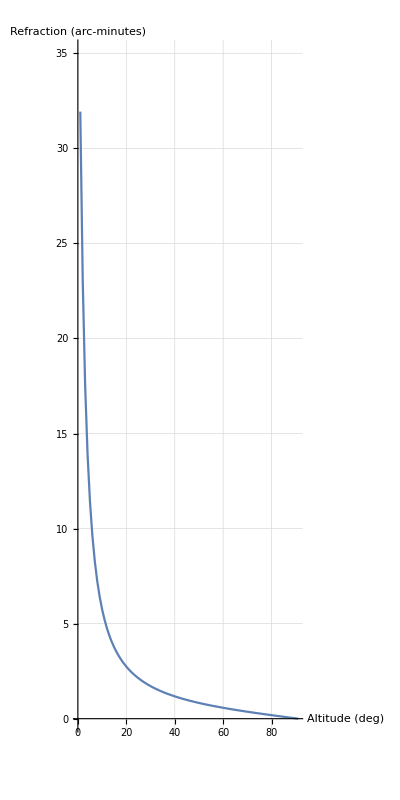

```mathematica
ListLinePlot[{31.932728402861514,23.091083084653214,17.546616078117175,13.914702549981147,11.41229273152488,9.61195171749111,8.268307060493864,7.233949725214905,6.416589403576425,5.756243578980094,5.21259844440884,4.757738444851781,4.371814523843284,4.04037786599254,3.7526890244273594,3.5006160087619467,3.27789818939995,3.079643392707726,2.901977222557616,2.741793942332064,2.5965764799534647,2.4642643463601304,2.343155328924256,2.231831363425585,2.129101963307582,2.0339605673613788,1.945550508627257,1.8631382308877962,1.7860920220595966,1.713864988539392,1.6459813198260653,1.5820251272600951,1.5216313136203183,1.4644780561550053,1.4102805813482142,1.358785980252915,1.3097688675854768,1.263027729136602,1.2183818334458851,1.175668609247033,1.1347414085871272,1.0954675912052383,1.05772687785187,1.0214099293682064,0.9864171163724892,0.9526574504132563,0.9200476522600876,0.8885113374702877,0.8579783021851197,0.8283838950629205,0.7996684635353581,0.7717768641879322,0.7446580289165139,0.7182645792819293,0.6925524832108704,0.6674807484685035,0.6430111484113231,0.6191079761406032,0.5957378235630502,0.572869382478981,0.550473265069485,0.5285218417631723,0.5069890941276196,0.4858504815355594,0.4650828198772387,0.444664171001436,0.42457374181570395,0.40479179197335474,0.3852995492548506,0.3660791318924788,0.34711347703757417,0.3283862748145818,0.30988190732381343,0.29158539222267965,0.2734823302151919,0.25555885626119,0.2378015940503485,0.22019761328983167,0.20273438973918695,0.1853997674993632,0.16818192346959715,0.15106933364240754,0.13405074102143727,0.11711512504458965,0.10025167228116899,0.08344974817707845,0.066698869858762,0.04998867965239012,0.03330891921294932,0.016649404338042018,0.},AxesLabel->{"Altitude (deg)","Refraction (arc-minutes)"},AspectRatio->2,PlotRange->{Automatic,{0,35}},GridLines->Automatic]
```